```mathematica
Lecture 8: Linear Algebra
```

Key linear algebra functions include:

```mathematica
{Table,MatrixForm,MatrixPlot,Dot,MatrixPower,N,Chop,Inverse,IdentityMatrix,Transpose,Det,Eigenvalues,Eigenvectors,Eigensystem,Norm,Normalize,LinearSolve,Solve,RowReduce,NullSpace,Dimensions,Orthogonalize}
```

```mathematica
M=Table[1/(i+j),{i,10},{j,10}]
```

{{1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11},{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12},{1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13},{1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14},{1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15},{1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16},{1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17},{1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18},{1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19},{1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20}}

```mathematica
Eigenvalues@N@M//Chop
```

{1.28766,0.162737,0.0132489,0.000798037,0.0000358996,1.19264×10^-6,2.8445×10^-8,4.61135×10^-10,0,0}

```mathematica
Eigensystem@M//N
```

{{1.28766,0.162737,0.0132489,0.000798037,0.0000358996,1.19264×10^-6,2.8445×10^-8,4.61135×10^-10,4.55322×10^-12,2.06752×10^-14},{{3.51697,2.66912,2.17856,1.85144,1.61502,1.43497,1.29267,1.17705,1.08107,1.},{-2.31909,-0.446227,0.322524,0.68698,0.869965,0.961372,1.00303,1.01636,1.01309,1.},{1.12156,-1.2044,-1.15652,-0.706308,-0.24817,0.136791,0.442184,0.679148,0.861137,1.},{-0.436126,1.41443,-0.00888405,-0.757306,-0.873293,-0.644253,-0.260825,0.172073,0.600822,1.},{0.144555,-0.944003,1.13082,0.683055,-0.215343,-0.747503,-0.787295,-0.426395,0.206352,1.},{-0.0422651,0.471751,-1.33178,0.668036,1.01078,0.181697,-0.67768,-0.92213,-0.349408,1.},{0.0111423,-0.193593,0.965017,-1.66395,0.259664,1.27816,0.389133,-0.948874,-1.09496,1.},{-0.00268903,0.0683521,-0.531478,1.72198,-2.23618,0.0674309,1.87016,0.103005,-2.06026,1.},{0.000600745,-0.0213606,0.241134,-1.2354,3.19881,-3.93599,0.854127,3.17495,-3.27681,1.},{-0.000125312,0.00602301,-0.0940842,0.699384,-2.88833,7.11732,-10.7106,9.64815,-4.7777,1.}}}

```mathematica
IdentityMatrix@6//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

### Exercise Subsection

a. Define BinomialMatrix[n_] be the (n+1)x(n+1) matrix with i,j entry equal to Binomial[i+j,i] where both i and j range from 0 to n.

```mathematica
BinomialMatrix[n_]:=Table[Binomial[i+j,i],{i,0,n},{j,0,n}]
```

```mathematica
MatrixForm@BinomialMatrix[6]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 3 | 4 | 5 | 6 | 7
1 | 3 | 6 | 10 | 15 | 21 | 28
1 | 4 | 10 | 20 | 35 | 56 | 84
1 | 5 | 15 | 35 | 70 | 126 | 210
1 | 6 | 21 | 56 | 126 | 252 | 462
1 | 7 | 28 | 84 | 210 | 462 | 924)

b. Use Det to determine that this matrix has an inverse for values of n between 0 and 100 and then create an animation of MatrixPlot for the Inverse of this matrix as n ranges from 0 to 100.

```mathematica
Det@BinomialMatrix[#]&/@Range[0,100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
ListAnimate[MatrixPlot@Inverse@BinomialMatrix[#]&/@Range[0,100]]
```

c. Let b be the vector in R^(11) with nth coordinate equal Sin[Pi n/2] for 0 <= n <= 10.  Solve the linear system BinomialMatrix[10].x = b for the vector x a few different ways (consider LinearSolve, Inverse,  Solve, and RowReduce).

```mathematica
b=Table[{Sin[Pi n/2]},{n,0,10}]
```

{{0},{1},{0},{-1},{0},{1},{0},{-1},{0},{1},{0}}

```mathematica
Inverse@BinomialMatrix[10].b
```

{{-33},{351},{-1696},{4706},{-8316},{9860},{-8000},{4408},{-1584},{336},{-32}}

```mathematica
LinearSolve[BinomialMatrix[10],b]
```

{{-33},{351},{-1696},{4706},{-8316},{9860},{-8000},{4408},{-1584},{336},{-32}}

```mathematica
Solve[#==0&/@(Flatten[BinomialMatrix[10].Table[{Subscript[x,i]},{i,0,10}]]-Flatten@b),Table[Subscript[x,i],{i,0,10}]]
```

{{x_0→-33,x_1→351,x_2→-1696,x_3→4706,x_4→-8316,x_5→9860,x_6→-8000,x_7→4408,x_8→-1584,x_9→336,x_10→-32}}

```mathematica
Transpose@Join[Transpose[BinomialMatrix[10]],Transpose@b]//RowReduce//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -33
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 351
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1696
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4706
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -8316
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 9860
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -8000
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4408
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1584
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 336
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -32)

### Exercise Subsection

a. The next cell defines a function MatrixPolynomial[poly_,x_,matrix_] with input a polynomial poly in the variable x, such as x^3-x^2+4x+5, and a square matrix matrix.  What is the output?

```mathematica
MatrixPolynomial[poly_,x_,matrix_]:=Sum[Coefficient[poly,x,i] MatrixPower[matrix,i],{i,0,Exponent[poly,x]}]
```

```mathematica
MatrixPolynomial[x^2+x+1,x,{{1,1},{1,2}}]
```

{{4,4},{4,8}}

```mathematica
CharacteristicPolynomial[{{1,1},{1,2}},λ]
```

1-3 λ+λ^2

b. Let mat be 10x10 matrix with random integer entries in between -10 and 10.  What is the result when evaluating MatrixPolynomial when taking the poly to be the CharacteristicPolynomial[mat,x] and taking matrix to be mat?

### Exercise Subsection

a. Define a function ProjectionMatrix[v__]  that has input any number of vectors of the same dimension (the double blank input v__ allows one or more vectors as input to the function because the double blank pattern matches one or more expressions) and outputs the projection matrix onto the span of the vectors in v.  

This projection matrix can be found with these steps: 
1. Use Orthogonalize to find an orthonormal basis for the span of the vectors in v (this implements the Gram-Schmidt procedure).
2. If the nonzero vectors in in the orthonormal basis are u_1,u_2,...,u_k then the desired projection matrix is Partition[u_1,1].{u_1}/(u_1.u_1)+...+Partition[u_k,1].{u_k}/(u_k.u_k)

b. Let P be the ProjectionMatrix found by selecting 5 vectors in R^10 at with random integer entries between -100 and 100 and then applying ProjectionMatrix to these 5 vectors.  Verify that the following properties hold:
1. The determinant of P is 0.
2. P^2 = P.
3. P is a symmetric matrix, meaning that P is equal to its transpose.
4. The inverse to I + P/2 is I - P/3.

```mathematica
v1={{1},{1},{1}};
v2={{1},{2},{3}};
v3={{2},{3},{4}};
```

```mathematica
ProjectionMatrix[v__]:=Apply[Plus,Partition[#,1].{#}/(#.#)&/@Cases[Orthogonalize[Flatten/@{v}],w_/;Norm@w!=0]]
```

```mathematica
ProjectionMatrix[v1,v2,v3]
```

{{5/6,1/3,-1/6},{1/3,1/3,1/3},{-1/6,1/3,5/6}}

```mathematica
P=ProjectionMatrix@@Table[Partition[RandomInteger[{-100,100},10],1],5];
```

```mathematica
Det@P
```

0

```mathematica
Dot[P,P]==P
```

True

```mathematica
Transpose@P==P
```

True

```mathematica
Dimensions@P
```

{10,10}

```mathematica
Inverse[IdentityMatrix@10+P/2]==(IdentityMatrix@10-P/3)
```

True

### Exercise Subsection

a. Write a function RandomSymmetric[n_] which generates an n x n symmetric matrix with entries that are random real numbers between 0 and 1.

```mathematica
RandomSymmetric[n_]:=Module[{A=Table[If[i<j,Random[],0],{i,n},{j,n}]},A+Transpose@A+Table[If[i==j,Random[],0],{i,n},{j,n}]]
```

b. Define a function called TestValue[A_] that uses a Module to define a local variable x such that x is a randomly selected unit vector the correct dimension to evaluate the matrix multiplication x.A.x (see Dimensions and Normalize).  The output of TestValue is the quantity x.A.x (this quantity is the matrix multiplication x^T A x, Mathematica automatically interprets the matrix multiplication correctly without the transpose on the first vector x).

```mathematica
TestValue[A_]:=Module[{x=Normalize@Table[Random[],First@Dimensions@A]},x.A.x]
```

c. Let A be a fixed symmetric 5x5 matrix, generated with RandomSymmetric[5].  Estimate the maximum value of the quantity x.A.x by running TestValue[A] many times and selecting the largest output.  Compare this with the largest Eigenvalue of A.

```mathematica
A=RandomSymmetric[5]
```

{{0.898176,0.919454,0.516491,0.979425,0.813012},{0.919454,0.549378,0.689202,0.125311,0.713134},{0.516491,0.689202,0.168044,0.267926,0.550713},{0.979425,0.125311,0.267926,0.797742,0.439306},{0.813012,0.713134,0.550713,0.439306,0.896775}}

```mathematica
Max@Table[TestValue[A],1000000]
```

3.20112

```mathematica
Eigenvalues@A
```

{3.20206,0.744955,-0.557573,-0.205005,0.125679}

### Exercise Subsection

Write a function RealEigenvectors with input a square matrix and output a list of linearly independent nonzero real eigenvectors of the matrix (removing any zero vectors or complex valued eigenvalues from Eigenvectors).  Additionally, any output vectors should be scaled to have length 1 (see Normalize).

### Exercise Subsection

Define a function PlotMatrixEffect[matrix_] where the input matrix is a 2x2 matrix.  The output should be a graphic that illustrates the effect of matrix multiplication by matrix on the unit circle and the vectors {1,0} and {0,1} in R^2.

```mathematica
PlotMatrixEffect[matrix_]:=Show[ParametricPlot[matrix.{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->{-2,2}],
Graphics[{Darker@Green,Thickness[.02],Arrow[{{0,0},matrix.{1,0}}],
Orange,Arrow[{{0,0},matrix.{0,1}}]}]]
```

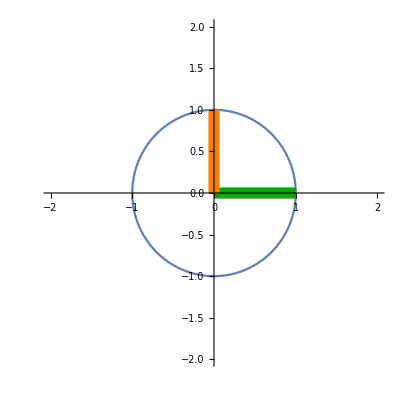

```mathematica
PlotMatrixEffect[IdentityMatrix@2]
```

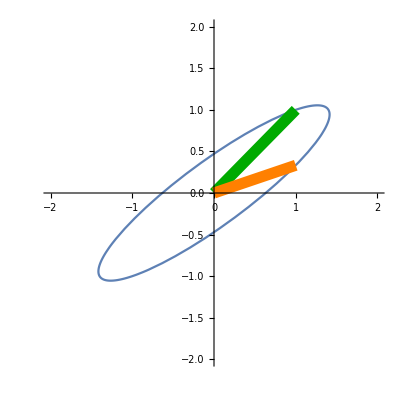

```mathematica
PlotMatrixEffect[{{1,1},{1,1/3}}]
```

### Exercise Subsection

a. The singular value decomposition (SVD) can be used to find low rank approximations of a matrix. 

The SVD is way to write a matrix A as U.S.V where U and V are matrices equal to their own conjugate transpose and S is a rectangular diagonal matrix.  The number of nonzero entries in S is the rank of the matrix A.  Experiment with Mathematica’s SingularValueDecomposition command for various matrices.

b. Consider the image loaded in the next cell:

```mathematica
dali=Import["https://anthonymendes.github.io/Dali.jpg"]
```

The command “ImageData” will convert this to a matrix with entries the darkness of the pixel on a scale of 0 to 1.  Change the image using the SVD to a lower rank matrix to see the effect of low rank approximations, see the next cell:

```mathematica
LowRankApproximation[image_,r_]:=
Module[{U,S,V},
{U,S,V}=SingularValueDecomposition[ImageData@image,r];
Image[U.S.Transpose@V]]
```